# Physics 234 PS#7(B) Eden Model: Border versus Area

Ziyang Gao
4/18/2018

## Section 1: What is the problem about

This problem is about investigating the Eden Model and trying to determine how the number of sites b in the border of the cluster depends on the number of sites n in the cluster itself. In particular, you will assume that b = cn^d, and then estimate the best values and uncertainties for log[c] and d.

## Section 2: Statistical functions

```mathematica
ave[myList_]:=Total[myList]/Length[myList]//N;
aveSqr[myList_]:=Total[myList^2]/Length[myList]//N;
var[myList_]:=aveSqr[myList]-ave[myList]^2;
unc[myList_]:=Sqrt[var[myList]/Length[myList]];
```

## Section 3: Develop a module for generating sizeList

Code for a single growth:

```mathematica
Clear[growCells]
growCells[oldCells_]:=
Module[
{choices,oldCluster,oldBorder,newSite,nnNewSite,tempBorder,newBorder,newCluster,newCells},
	
choices={{1,0},{0,1},{-1,0},{0,-1}};
oldCluster=oldCells[[1]];
oldBorder=oldCells[[2]];
newSite=oldBorder[[RandomInteger[{1,Length[oldBorder]}]]];
newCluster=Join[oldCluster,{newSite}];
nnNewSite=Map[(#+newSite)&,choices];
tempBorder=Union[oldBorder,nnNewSite];
newBorder=Complement[tempBorder,newCluster];

newCells={newCluster,newBorder}		
];
```

A for-loop generating sizeList of 1000 times of growth:

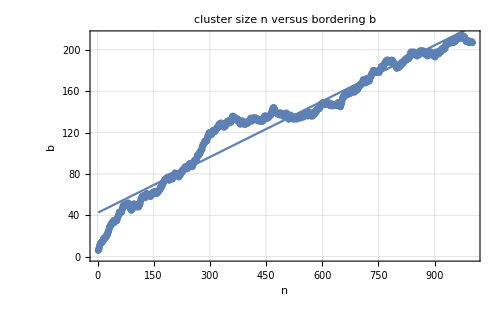

General::munfl: 0.233987^499. is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0480674^499. is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
1 | 42.348 | 0.740875 | 57.1594 | 4.85823×10^-317
x | 0.18 | 0.00128035 | 140.586 | 0.

0.18 x+42.348

{0.740875,0.00128035}

```mathematica
oldCells={{{0,0}},{{1,0},{-1,0},{0,1},{0,-1}}};
sizeList = {};
For[i=1,i≤1000,i++,
newPic=growCells[oldCells];
clusterArea = Length[newPic[[1]]];
borderArea = Length[newPic[[2]]];
AppendTo[sizeList,{clusterArea,borderArea}];
oldCells= {newPic[[1]],newPic[[2]]};
];
plot1=ListPlot[sizeList,PlotStyle->{Blue[1,0,0],PointSize[0.01]},Frame->True,FrameLabel->{"n","b"},PlotRange->All,PlotLabel->Style["cluster size n  versus  bordering b",FontFamily->"Helvetica",FontSize->12,FontWeight->"Bold"],GridLines->Automatic,ImageSize->500];
model=LinearModelFit[sizeList,x,x];
plot2 =Plot[model["BestFit"],{x,2,1000}];
Show[plot1,plot2]
model["ParameterTable"]
model["BestFit"]
model["ParameterErrors"]
```

## Section 4: Develop a module that applies Fit[] to the log of sizeList

In this section we will compute Log of sizeList from section 3 and a fitted model for logSizeList. We take out the first 50 data points because the power-law relationship may only hold from a large n values.

0.579415 x+1.33774

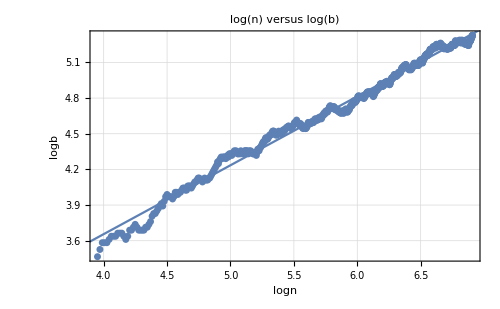

```mathematica
logSizeList=Map[Log,sizeList,{2}]//N;
logSizeList=Take[logSizeList,-950];
plot3=ListPlot[logSizeList,PlotStyle->{Blue[1,0,0],PointSize[0.01]},Frame->True,FrameLabel->{"logn","logb"},PlotRange->All,PlotLabel->Style["log(n)  versus  log(b)",FontFamily->"Helvetica",FontSize->12,FontWeight->"Bold"],GridLines->Automatic,ImageSize->500];
model2=Fit[logSizeList,{1,x},x]
plot4 =Plot[model2,{x,1,1000}];
Show[plot3,plot4]
```

## Section 5 : Create a list of {log[c], d} and find their statistical parameters

We generate sizeListList below as a list of 100 {log[c], d} vales, then fit a linear model to the values and calculate their mean and standard deviation values.

```mathematica
sizeListList={};
For[m=1,m≤100,m++,oldCells={{{0,0}},{{1,0},{-1,0},{0,1},{0,-1}}};
sizeList = {};
For[i=1,i≤1000,i++,
newPic=growCells[oldCells];
clusterArea = Length[newPic[[1]]];
borderArea = Length[newPic[[2]]];
AppendTo[sizeList,{clusterArea,borderArea}];
oldCells= {newPic[[1]],newPic[[2]]};
]; 
logSizeList=Map[Log,sizeList,{2}]//N;
logSizeList=Take[logSizeList,-950];
model3=Fit[logSizeList,{1,x},x];
d =model3[[2]]/x;
logc=model3[[1]];
AppendTo[sizeListList,{d,logc}];
]
sizeListList[[1]]
```

{0.59288,1.34416}

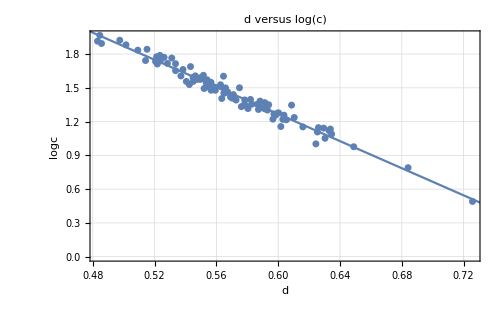

| Estimate | Standard Error | t-Statistic | P-Value
1 | 4.88082 | 0.0632848 | 77.1248 | 1.53469×10^-89
x | -6.02245 | 0.111117 | -54.1993 | 7.1216×10^-75

4.88082-6.02245 x

{0.0632848,0.111117}

{0.568067,1.45967}

{0.0410536,0.251334}

```mathematica
plot4=ListPlot[sizeListList,PlotStyle->{Blue[1,0,0],PointSize[0.01]},Frame->True,FrameLabel->{"d","logc"},PlotRange->All,PlotLabel->Style["d  versus  log(c)",FontFamily->"Helvetica",FontSize->12,FontWeight->"Bold"],GridLines->Automatic,ImageSize->500];
model4=LinearModelFit[sizeListList,{1,x},x];
plot5 =Plot[model4["BestFit"],{x,0,1}];
Show[plot4,plot5]
model4["ParameterTable"]
model4["BestFit"]
model4["ParameterErrors"]
Mean[sizeListList]
StandardDeviation[sizeListList]
```

From the above statistical measurements, we could conclude that the best value for d is 0.568, and the best value for log(c) is 1.460.

## Conclusion and Speculation

Based on our initial model speculation of log(b) = log(c) + d*log(n), the relation between log(b) and log(n) is log(b) = 1.460 + 0.568*log(n), resulting from a sample size of 100 generations each on a sizeList of 1000.